```mathematica
Clear["Global`*"];
```

```mathematica
(σ=Import[NotebookDirectory[]<>"CrossSection.xls"][[1,5;;,{12,15,16}]])//TableForm;
σe=Interpolation[σ[[All,{1,2}]],InterpolationOrder->1];
σa=Interpolation[σ[[All,{1,3}]],InterpolationOrder->1];
ListPlot[{σ[[All,{1,2}]],σ[[All,{1,3}]]},Joined->True,PlotRange->All];
Plot[{σe[λ],σa[λ]},{λ, σ[[1,1]], σ[[-1,1]]},PlotRange->All, ImageSize->Large];
```

```mathematica
c = 3×10^8; (* m/s *)
τ=1.45×10^-3; (* s *)
NN = 300; (* ppm *)
NN = 6.62×10^22 NN; (* 1/m^3 *)
h = 6.63×10^-34; (* Постоянная планка *)
Aeff = Pi/4 7^2×10^-12; (* эффективная площадь моды *)
L = 2;
```

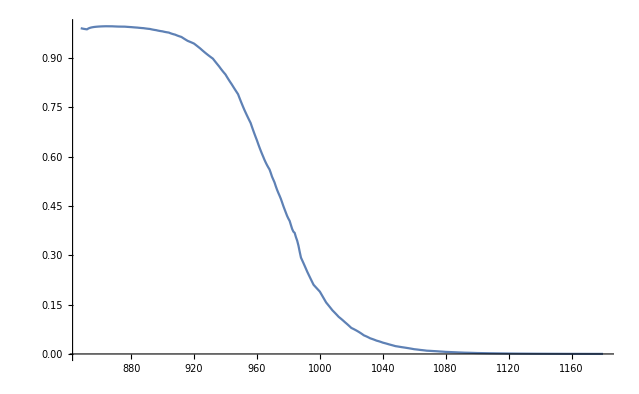

```mathematica
ListPlot[Parallelize[Table[
{λ,σa[λ]/(σa[λ]+σe[λ])},
{λ,σ[[1,1]],σ[[-1,1]],(σ[[2,1]]-σ[[1,1]])/5}]]
,Joined->True,PlotRange->All, ImageSize->Large]
```